```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Lev4DoppTestv[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.05]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi ((210.923*10^6) +(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/( 10^9),(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

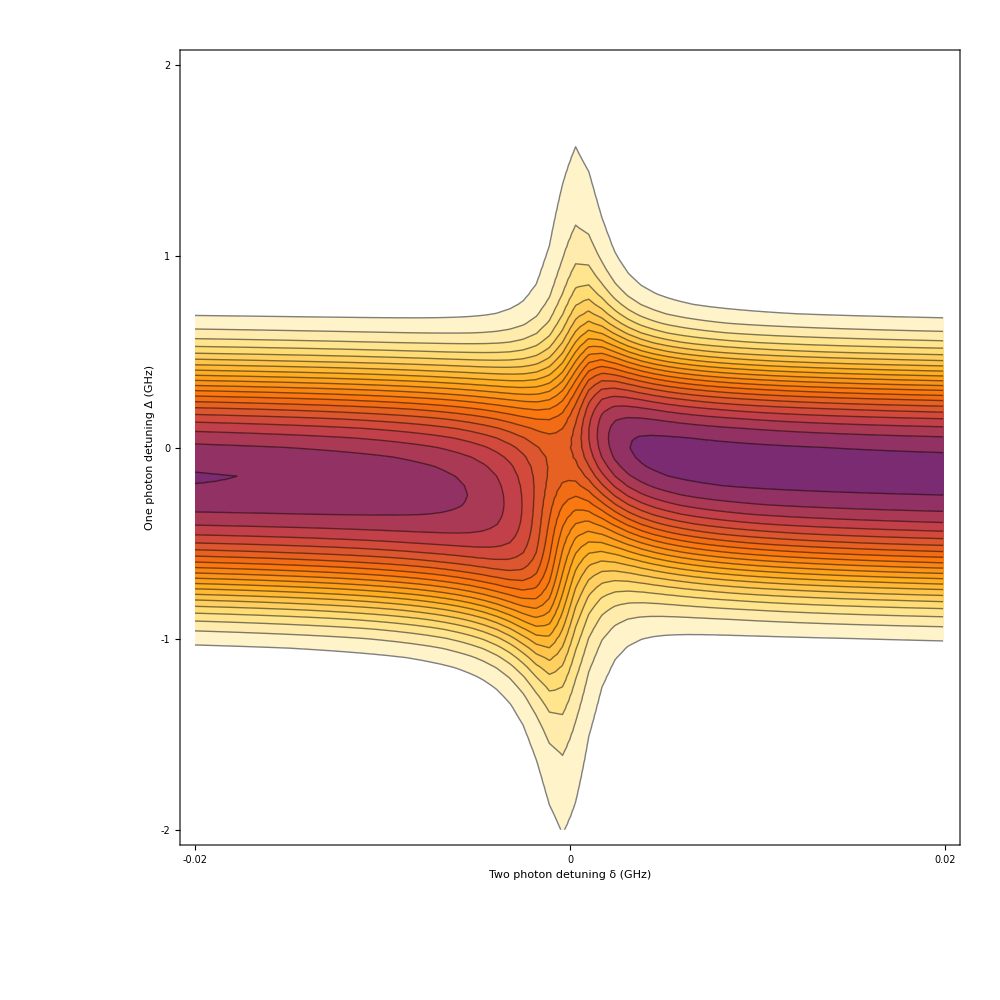

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv[47,10/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Range[-0.020,0.02,0.0007]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.02,0.02},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

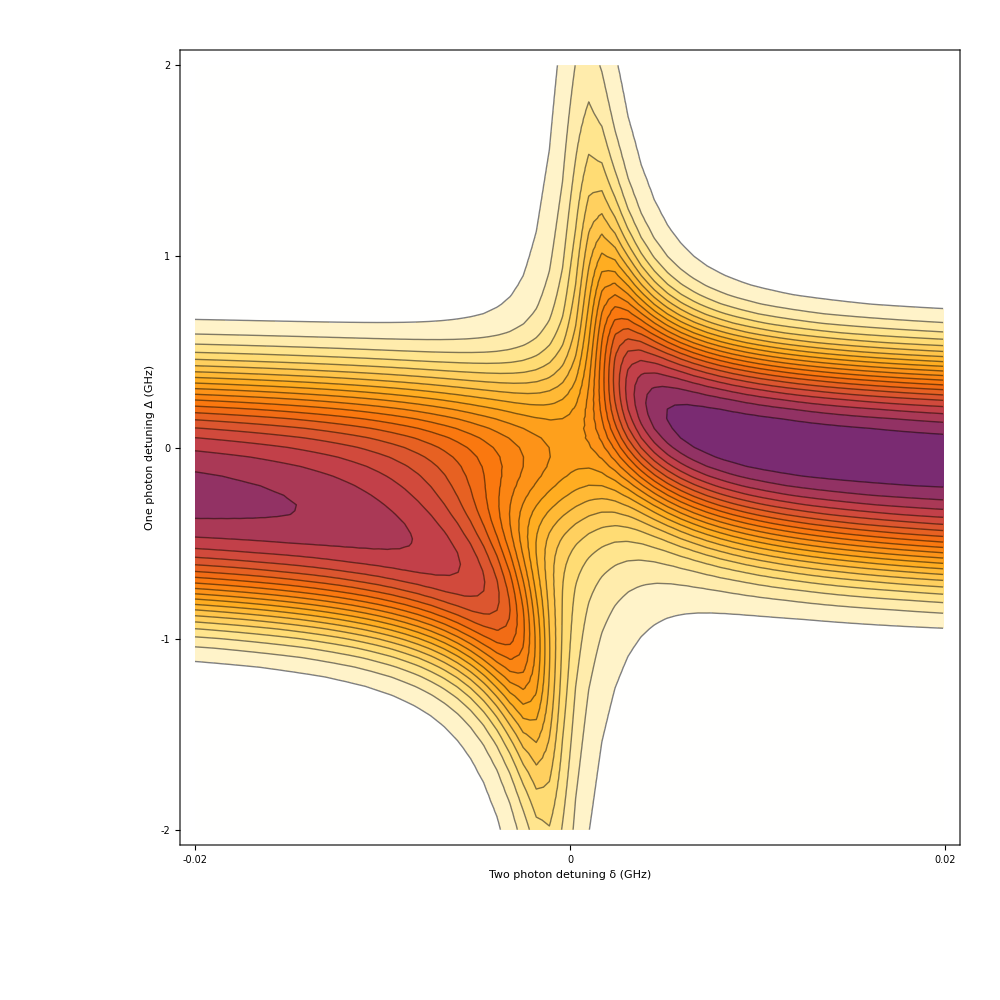

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv[47,35/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Range[-0.020,0.02,0.0007]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.02,0.02},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

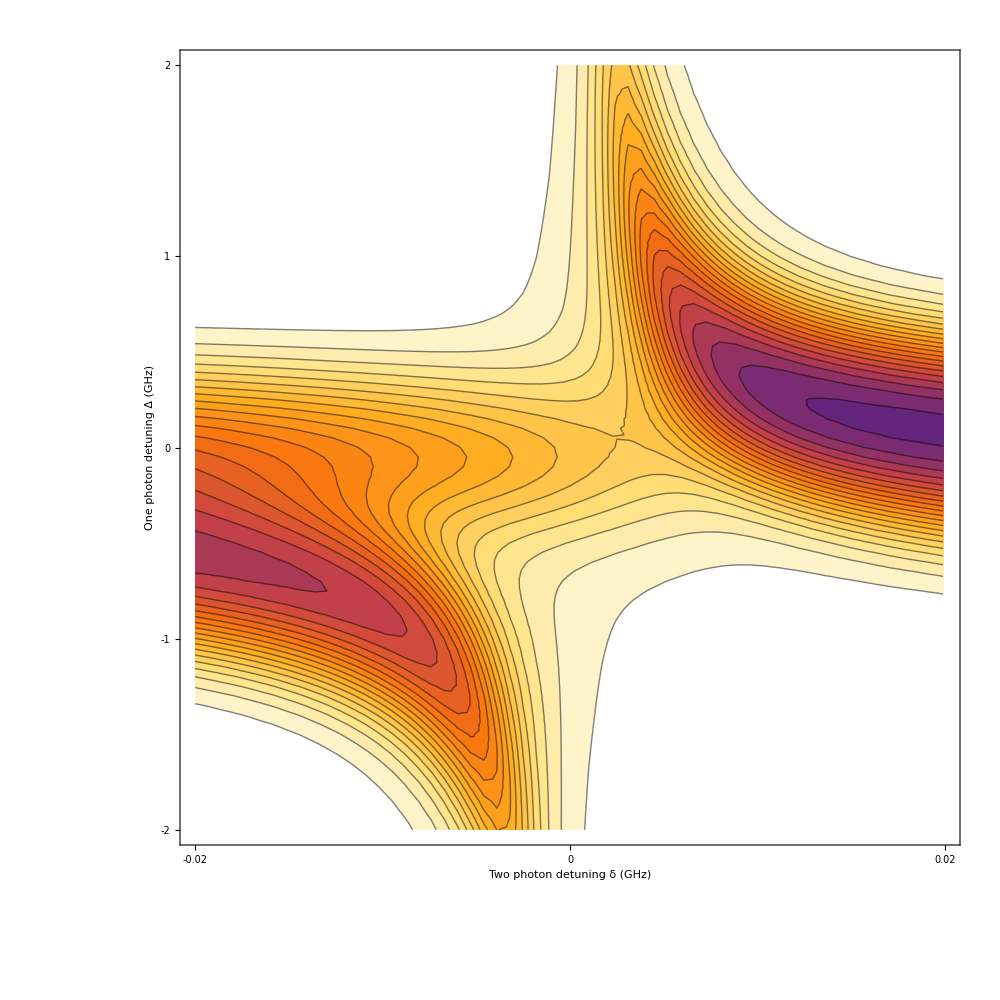

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv[47,100/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Range[-0.020,0.02,0.0007]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.02,0.02},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

```mathematica
Lev4DoppTestv87[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.05]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.7468 10^6/2;
γ42=2*Pi*5.7468 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/6]*2.5373 10^-29;
d42=Sqrt[1/6]*2.5373 10^-29;
d31=Sqrt[1/18]*2.5373 10^-29;
d41=Sqrt[5/18]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.9788509*10^-9);
wc=2Pi 377.1074635*10^12;
w43=2Pi ((306.246*10^6) +(510.410*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/( 10^9),(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

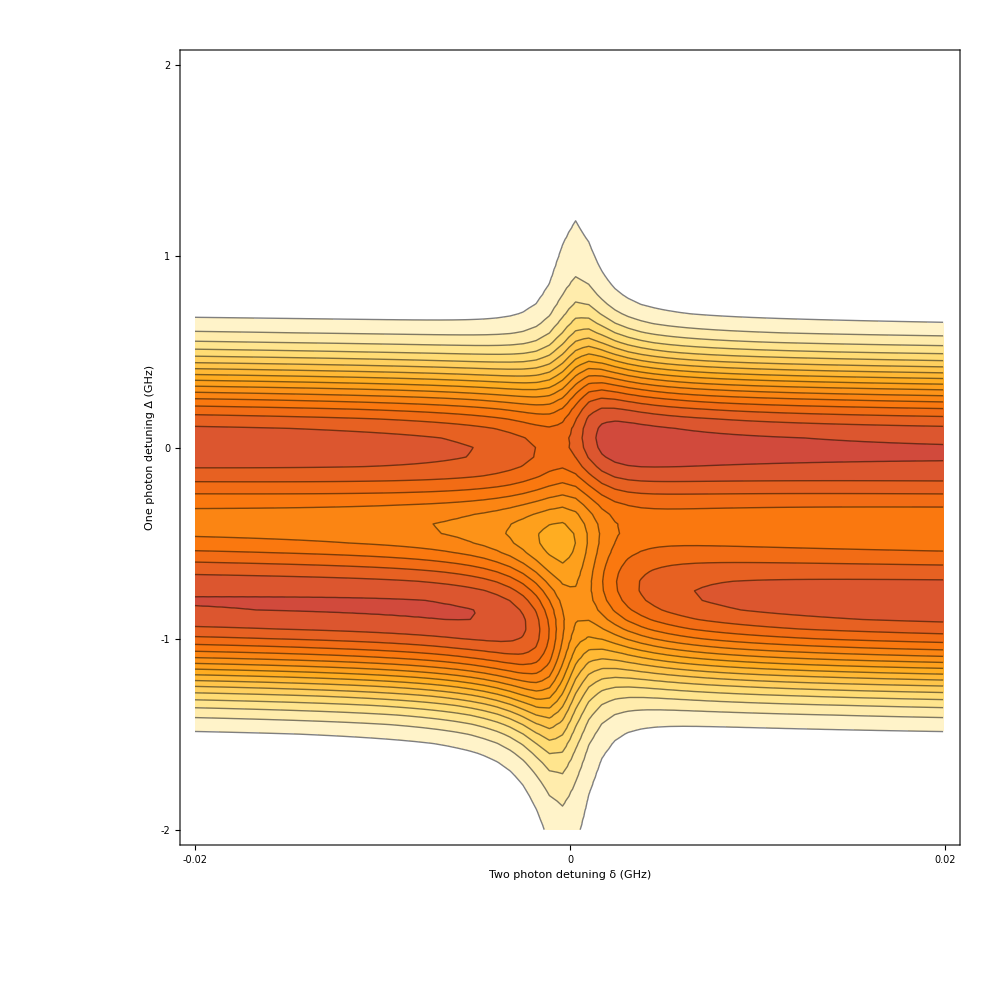

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv87[47,10/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Range[-0.020,0.02,0.0007]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.02,0.02},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

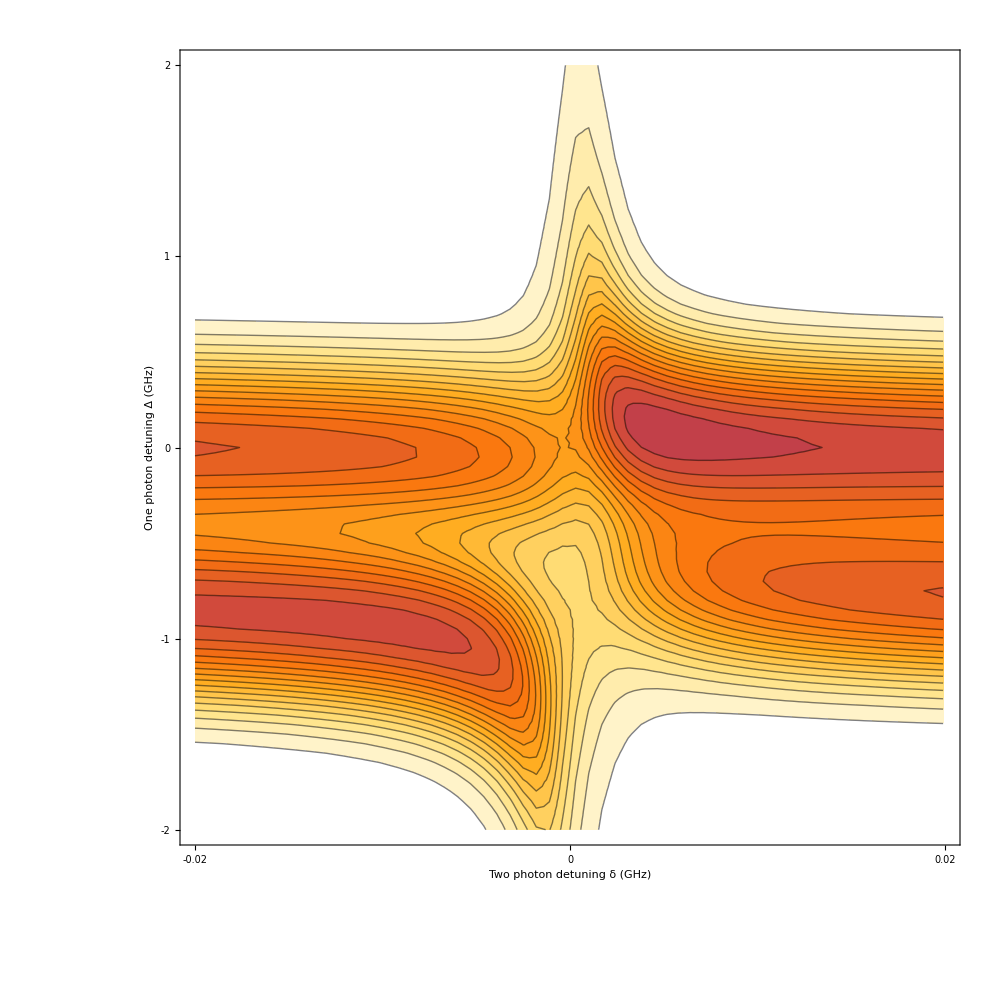

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv87[47,35/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Range[-0.020,0.02,0.0007]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.02,0.02},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

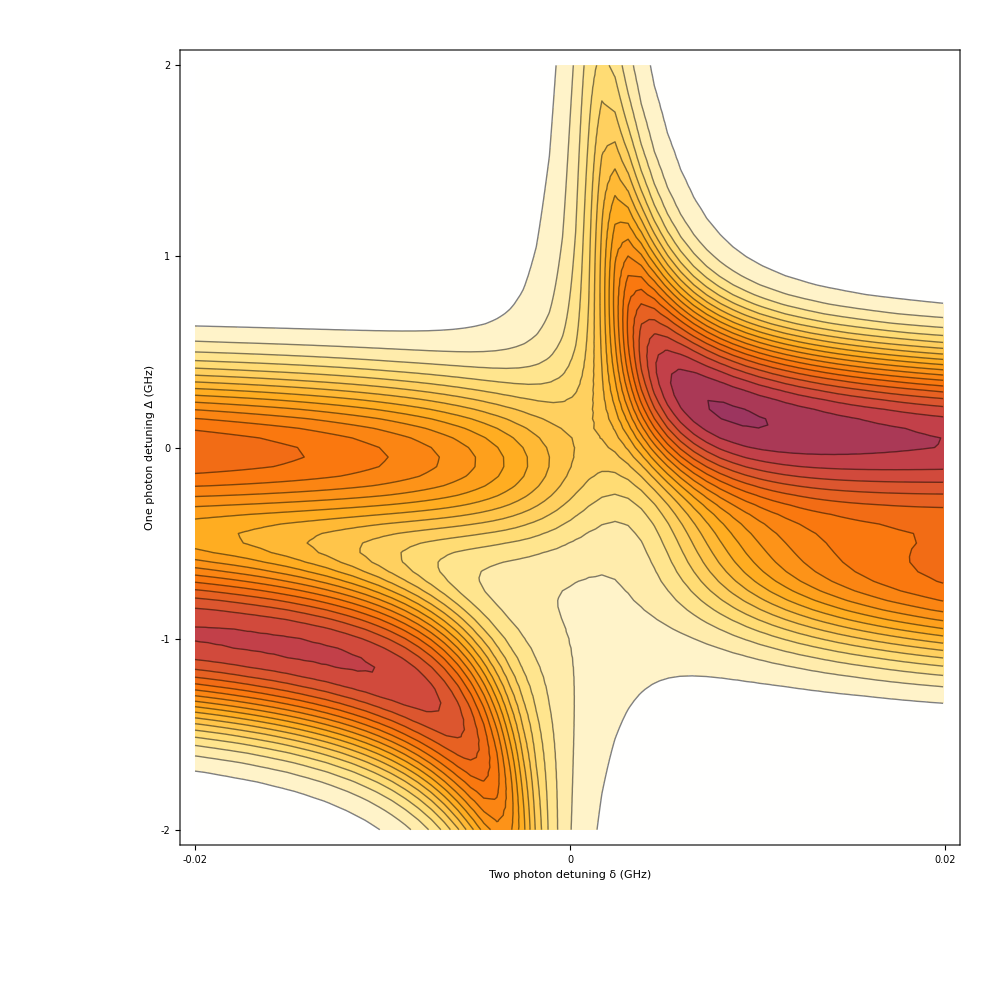

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv87[47,100/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Range[-0.020,0.02,0.0007]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.02,0.02},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

```mathematica
Lev4DoppTestvsc[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.2,0.2,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];

γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi ((210.923*10^6) +(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


Transpose[{d/( 10^9),
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

]
```

```mathematica
Lev4DoppTestv87sc[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.2,0.2,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.7468 10^6/2;
γ42=2*Pi*5.7468 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/6]*2.5373 10^-29;
d42=Sqrt[1/6]*2.5373 10^-29;
d31=Sqrt[1/18]*2.5373 10^-29;
d41=Sqrt[5/18]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.9788509*10^-9);
wc=2Pi 377.1074635*10^12;
w43=2Pi ((306.246*10^6) +(510.410*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



Transpose[{d/( 10^9),
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

]
```

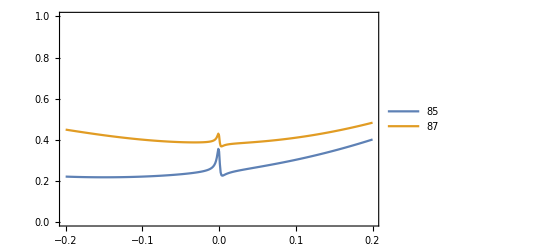

```mathematica
P=5;
γ=1.438;
ListPlot[
{Lev4DoppTestvsc[47,P/1000,1.0/1000,γ*10^6,0*10^9],Lev4DoppTestv87sc[47,P/1000,1.0/1000,γ*10^6,0*10^9]},Joined->True,Frame->True,Axes->False,PlotRange->{0,1},PlotLegends->{85,87}]
```

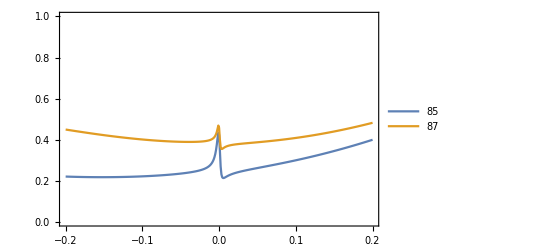

```mathematica
P=10;
γ=1.438;
ListPlot[
{Lev4DoppTestvsc[47,P/1000,1.0/1000,γ*10^6,0*10^9],Lev4DoppTestv87sc[47,P/1000,1.0/1000,γ*10^6,0*10^9]},Joined->True,Frame->True,Axes->False,PlotRange->{0,1},PlotLegends->{85,87}]
```

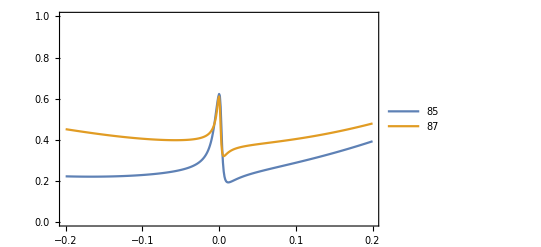

```mathematica
P=35;
γ=1.438;
ListPlot[
{Lev4DoppTestvsc[47,P/1000,1.0/1000,γ*10^6,0*10^9],Lev4DoppTestv87sc[47,P/1000,1.0/1000,γ*10^6,0*10^9]},Joined->True,Frame->True,Axes->False,PlotRange->{0,1},PlotLegends->{85,87}]
```

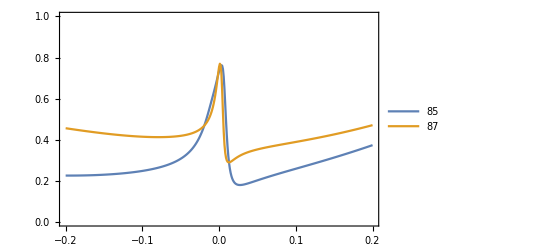

```mathematica
P=100;
γ=1.438;
ListPlot[
{Lev4DoppTestvsc[47,P/1000,1.0/1000,γ*10^6,0*10^9],Lev4DoppTestv87sc[47,P/1000,1.0/1000,γ*10^6,0*10^9]},Joined->True,Frame->True,Axes->False,PlotRange->{0,1},PlotLegends->{85,87}]
```

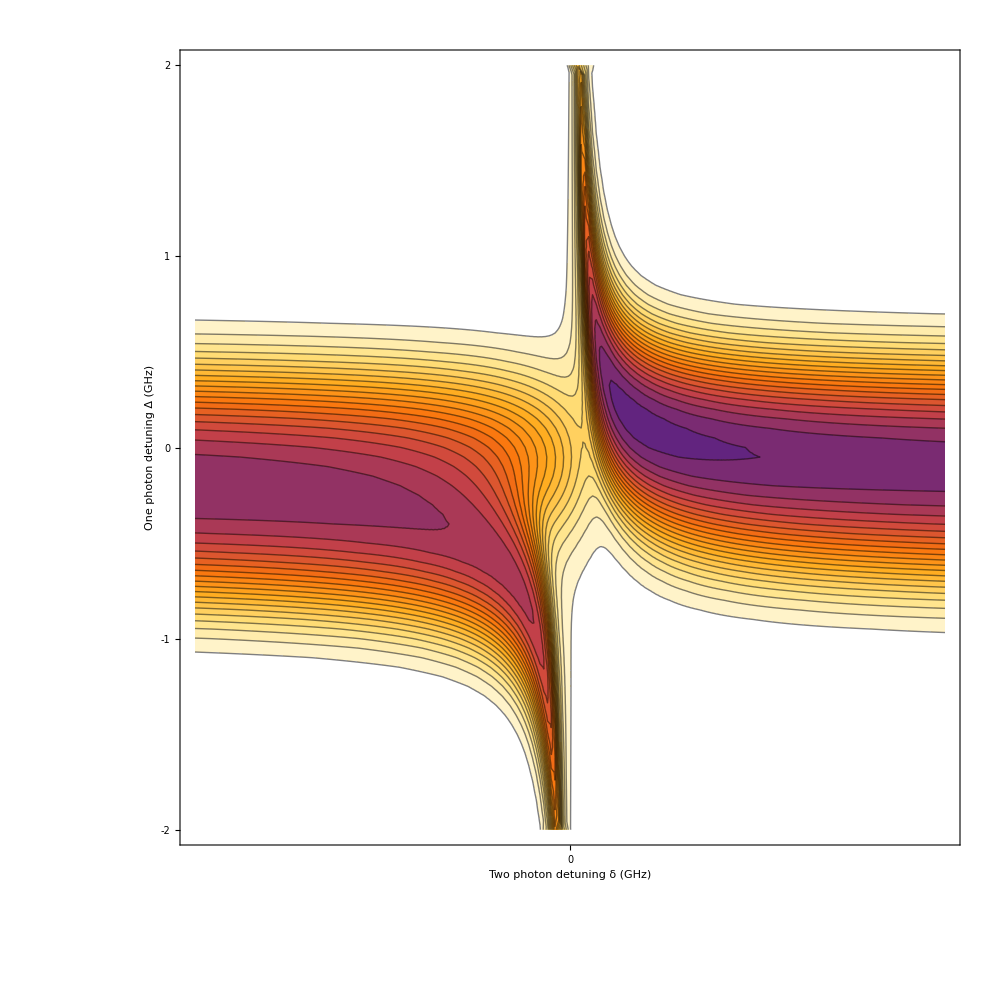

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv[47,10/1000,1.0/1000,0.1*10^6,delt*10^9,1,0]}],{delt,
Range[-0.010,0.01,0.0001]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.01,0.01},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

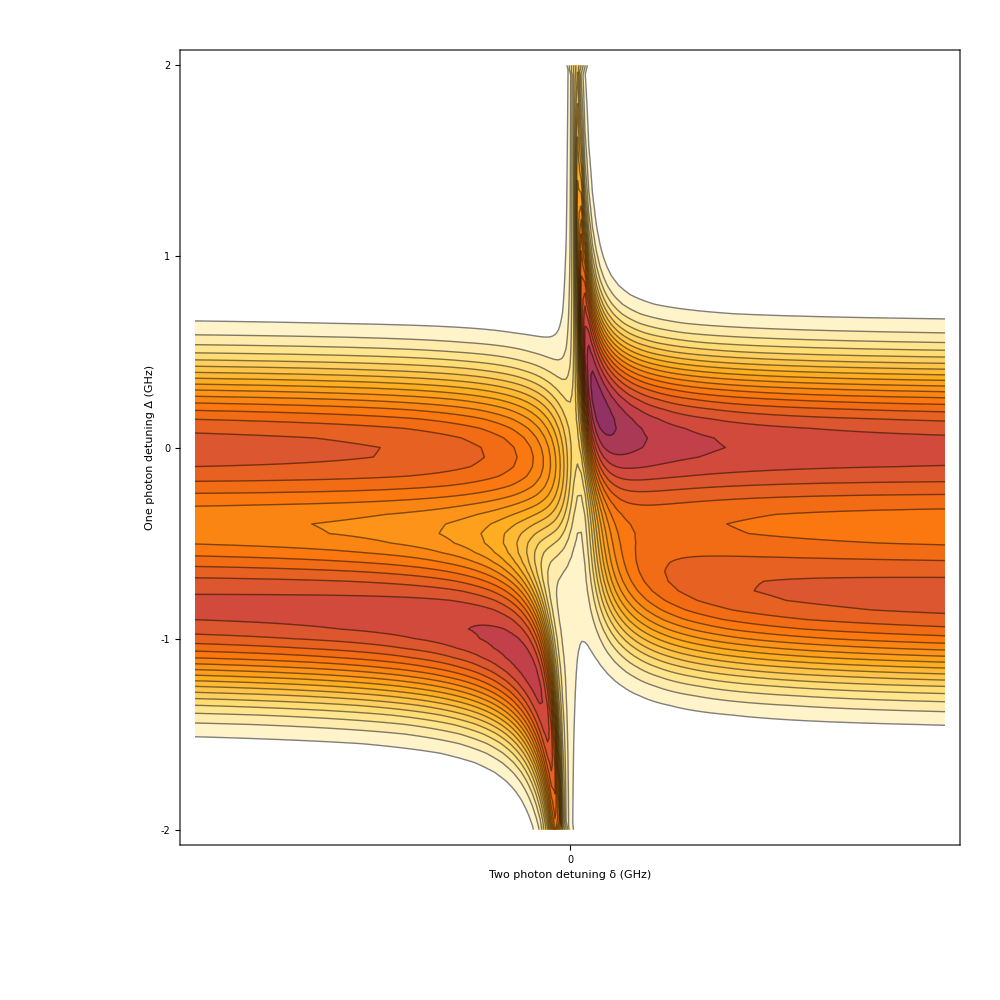

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,81}],Lev4DoppTestv87[47,10/1000,1.0/1000,0.1*10^6,delt*10^9,1,0]}],{delt,
Range[-0.010,0.01,0.0001]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.01,0.01},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=1.4
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Print[p];
Tvw41={};Tvw31={};
Do[
list=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,361];
list1=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,361];

list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,816];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,816];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41=Append[Tvw41,{p,1-EIT1/ABS1}];
Tvw31=Append[Tvw31,{p,1-EIT/ABS}];

,{p,0,100,1}]
]
```

1.4

15.865

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

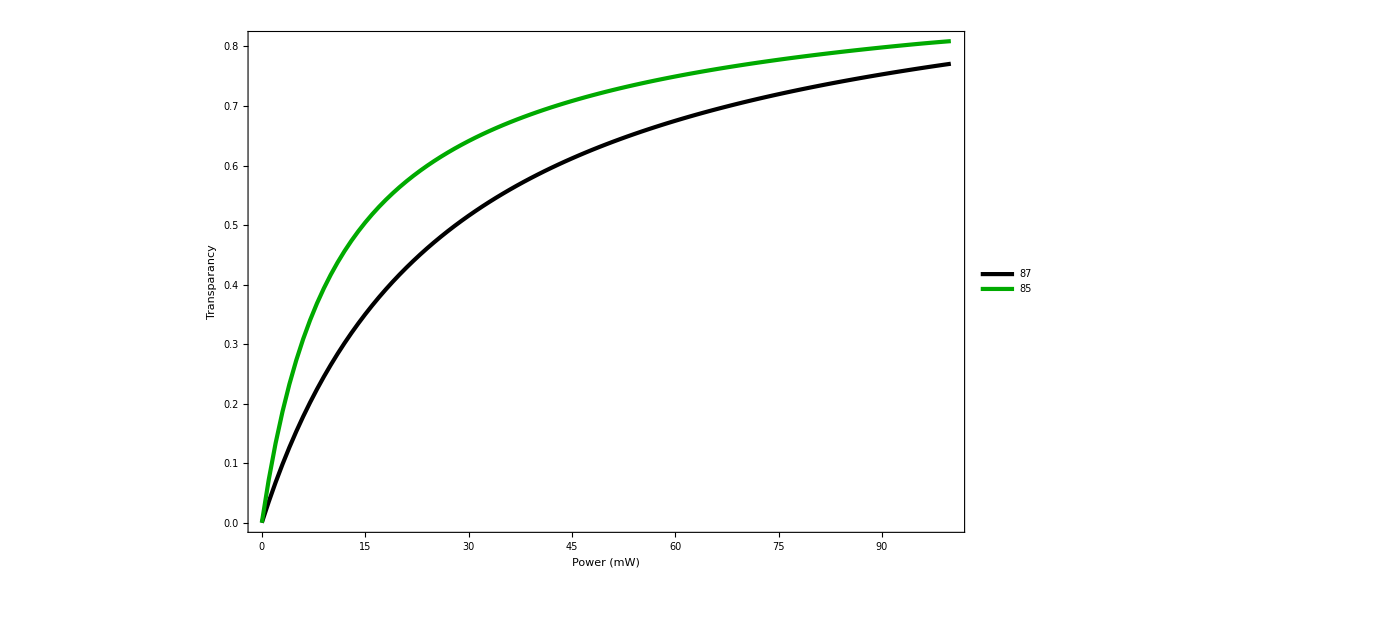

```mathematica
ListPlot[{Tvw41,Tvw31},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Brown]
,Dashed},{AbsoluteThickness[3],Purple,Dashed}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=3
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Print[p];
Tvw41={};Tvw31={};
Do[
list=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,361];
list1=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,361];

list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,816];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,816];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41=Append[Tvw41,{p,1-EIT1/ABS1}];
Tvw31=Append[Tvw31,{p,1-EIT/ABS}];

,{p,0,100,10}]
]
```

3

15.865

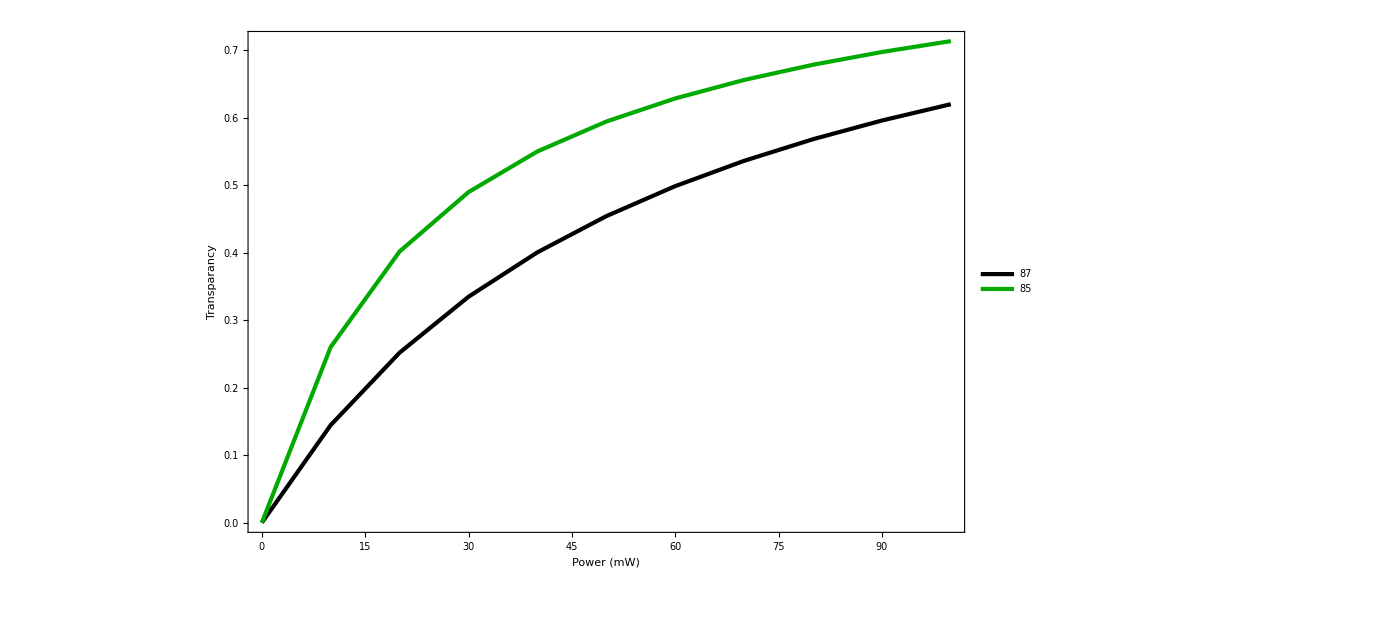

```mathematica
ListPlot[{Tvw41,Tvw31},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Brown]
,Dashed},{AbsoluteThickness[3],Purple,Dashed}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=42;
γ=1.4
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Print[p];
Tvw41={};Tvw31={};
Do[
list=Lev4DoppTestsc[T,p/1000,0.9/1000,γ*10^6,0,0,361];
list1=Lev4DoppTestsc[T,0/1000,0.9/1000,γ*10^6,0,0,361];

list3=Lev4DoppTestsc[T,p/1000,0.9/1000,γ*10^6,0,0,816];
list4=Lev4DoppTestsc[T,0/1000,0.9/1000,γ*10^6,0,0,816];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41=Append[Tvw41,{p,1-EIT1/ABS1}];
Tvw31=Append[Tvw31,{p,1-EIT/ABS}];

,{p,0,100,10}]
]
```

1.4

15.865

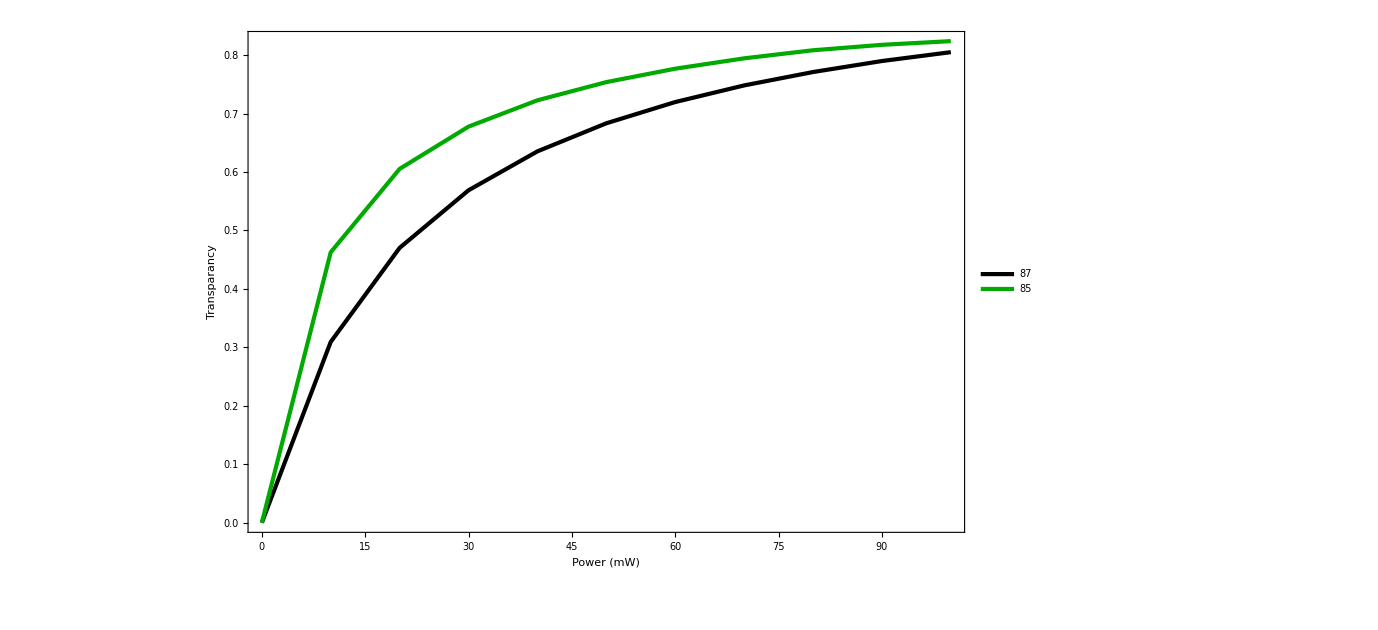

```mathematica
ListPlot[{Tvw41,Tvw31},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Brown]
,Dashed},{AbsoluteThickness[3],Purple,Dashed}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}]
```